```mathematica
树叶的运动
```

```mathematica
树叶的随机运动观察
```

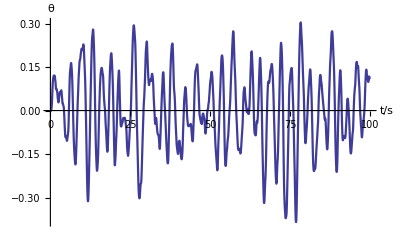

```mathematica
dis=NormalDistribution[0,1];
m=1000;δt=0.1;ω=2;α=0.5;time=(m-1)*δt;
f=Table[Random[dis],{m}];
f=Table[{δt*(i-1),f[[i]]},{i,m}];
f=Interpolation[f];
equ={θ''[t]+ω^2*θ[t]+α*θ'[t]==f[t],θ[0]==0,
θ'[0]==0};
s=NDSolve[equ,θ,{t,0,time},MaxSteps->∞];
Plot[θ[t]/.s[[1]],{t,0,time},PlotPoints->200,
AxesLabel->{"t/s","θ"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]
Clear[dis,m,ω,δt,f,equ,s,θ,time,α]
```

```mathematica
树叶的能量统计
```

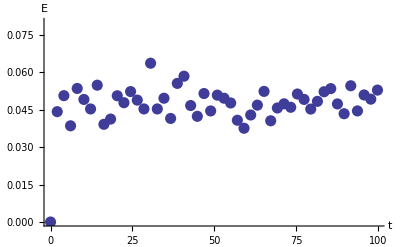

```mathematica
dis=NormalDistribution[0,1];
n=100;m=1000;δt=0.1;time=(m-1)*δt;
α=2.0;ω=2.0π;
fr=Table[RandomReal[dis],{i,n},{j,m}];
fr=Table[{δt*(i-1),fr[[j,i]]},{j,n},{i,m}];
fr=Table[Interpolation[fr[[i]]],{i,n}];
equ=Table[{θ''[t]+α*θ'[t]+ω^2*θ[t]==fr[[i]][t],
θ[0]==0,θ'[0]==0},{i,n}];
s=Table[NDSolve[equ[[i]],θ,{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];
sample=50;δt=time/(sample-1);result={};
Do[
ps=Table[θ[δt*(i-1)]/.s[[j]],{j,n}];
vs=Table[θ'[δt*(i-1)]/.s[[j]],{j,n}];
AppendTo[result,
{δt*(i-1),Sum[ω^2 ps[[j]]^2+vs[[j]]^2,{j,n}]/n}],
{i,sample}]
ListPlot[result,PlotStyle->PointSize[0.02],
PlotRange->{0,0.08},AxesLabel->{"t","E"},
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]
Clear[dis,time,fr,s,result,equ,ps,θ,α,ω]
```

```mathematica
显示向平衡的过渡
```

General::obspkg: "Statistics`NormalDistribution`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

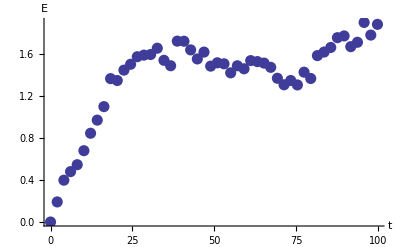

```mathematica
<<Statistics`NormalDistribution`
dis=NormalDistribution[0,1];
n=100;m=1000;δt=0.1;time=(m-1)*δt;
α=0.05;ω=2π;
fr=Table[Random[dis],{i,n},{j,m}];
fr=Table[{δt*(i-1),fr[[j,i]]},{j,n},{i,m}];
fr=Table[Interpolation[fr[[i]]],{i,n}];
equ=Table[{θ''[t]+α*θ'[t]+ω^2*θ[t]==fr[[i]][t],
θ[0]==0,θ'[0]==0},{i,n}];
s=Table[NDSolve[equ[[i]],θ,{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];
sample=50;δt=time/(sample-1);result={};
Do[ps=Table[θ[δt*(i-1)]/.s[[j]],{j,n}];
vs=Table[θ'[δt*(i-1)]/.s[[j]],{j,n}];
AppendTo[result,
{δt*(i-1),Sum[ω^2 ps[[j]]^2+vs[[j]]^2,{j,n}]/n}],
{i,sample}]
ListPlot[result,PlotStyle->PointSize[0.02],
PlotRange->All,AxesLabel->{"t","E"}]
Clear[dis,n,m,δt,time,fr,s,result,vs,ps,
θ,α,ω,equ]
```

```mathematica
粘滞力为0,500秒
```

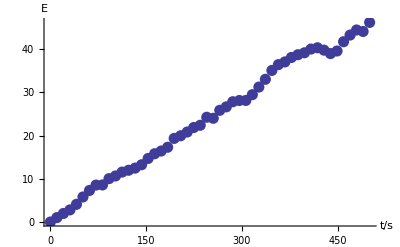

```mathematica
dis=NormalDistribution[0,1];
n=100;m=5000;δt=0.1;time=(m-1)*δt;
α=0;ω=2.0π;
fr=Table[Random[dis],{i,n},{j,m}];
fr=Table[{δt*(i-1),fr[[j,i]]},{j,n},{i,m}];
fr=Table[Interpolation[fr[[i]]],{i,n}];
equ=Table[{θ''[t]+α*θ'[t]+ω^2*θ[t]==fr[[i]][t],
θ[0]==0,θ'[0]==0},{i,n}];
s=Table[NDSolve[equ[[i]],θ,{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];
sample=50;δt=time/(sample-1);result={};
Do[ps=Table[θ[δt*(i-1)]/.s[[j]],{j,n}];
vs=Table[θ'[δt*(i-1)]/.s[[j]],{j,n}];
AppendTo[result,
{δt*(i-1),Sum[ω^2 ps[[j]]^2+vs[[j]]^2,{j,n}]/n}],
{i,sample}]
ListPlot[result,PlotStyle->PointSize[0.02],
PlotRange->All,AxesLabel->{"t/s","E"},
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]
Clear[dis,time,fr,s,result,equ,vs,ps]
```

```mathematica
粘滞力为0,转角统计
```

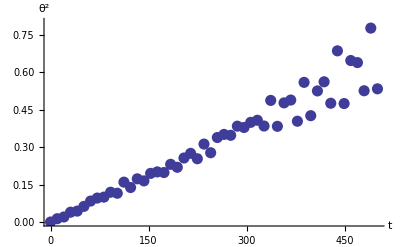

```mathematica
dis=NormalDistribution[0,1];
n=100;m=5000;δt=0.1;time=(m-1)*δt;
α=0;ω=2π;
fr=Table[RandomReal[dis],{i,n},{j,m}];
fr=Table[{δt*(i-1),fr[[j,i]]},{j,n},{i,m}];
fr=Table[Interpolation[fr[[i]]],{i,n}];
equ=Table[{θ''[t]+α*θ'[t]+ω^2*θ[t]==fr[[i]][t],
θ[0]==0,θ'[0]==0},{i,n}];
s=Table[NDSolve[equ[[i]],θ,{t,0,time},
MaxSteps->∞],{i,n}];
s=Flatten[s];
sample=50;δt=time/(sample-1);result={};
Do[ps=Table[θ[δt*(i-1)]/.s[[j]],{j,n}];
AppendTo[result,
{δt*(i-1),Sum[ ps[[j]]^2,{j,n}]/n}],{i,sample}]
ListPlot[result,PlotStyle->PointSize[0.02],
PlotRange->{0,0.8},AxesLabel->{"t","θ^2"},
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]
Clear[dis,n,m,δt,time,fr,ps,ω]
```